```mathematica
nota
```

# Intensity averaging of Rabi oscillation

## Gabriel Patenotte || October, 2021 || Ni Group

## Notebook setup

```mathematica
Remove["Global`*"] (*Clears all variables*)

padding={{70, 10}, {50, 10}}; (*Space around plots*)
size=500;   (*Size of plots*)

SetOptions[Plot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)

SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,FrameTicks->{Automatic,Automatic},ImagePadding->padding,ImageSize->size];  (*Sets ListPlots to have a certain look*)

messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; (*These two lines make the code auto-abort when the evaluation detects an error. Useful to quickly find whether code has an issue.*)
```

## Init

### se. Provides a parametric solution to the Schrodinger equation given a Hamiltonian in terms of the given parameters for a duration tmax0.

```mathematica
se[H0_,param0_,tmax0_]:=Module[{H=H0,param=Flatten[{param0}],tmax=tmax0},
ψ[t_]={c1[t],c2[t],c3[t],c4[t]};  (*Wavefunction in 4 state basis*)
init=ψ[0]=={1,0,0,0}; (*Population initially in the ground state*)
SE=ⅈ ψ'[t]==H.ψ[t];(*The Schodinger equation*)
sols=ParametricNDSolve[{SE,init},{c1,c2,c3,c4},{t,tmax0},param,PrecisionGoal->7,Method->"StiffnessSwitching"]]  (*The StiffnessSwitching method greatly improves evaluation time.*)
```

### findACShift. Numerically finds the two-photon resonance for a given Hamiltonian.

```mathematica
findACShift[H0_]:=Module[{H=H0},
sols=se[H,δ,.1μs];
p1[δ_]=Abs[(c1[δ]/.sols)[.1 μs]]^2;
acData=Table[{δ,p1[δ MHz]},{δ,-20,20,.5}];
parabola=Fit[acData,{1,x,x^2},x];
guess=Solve[D[parabola,x]==0,x]⟦1,1,2⟧;
acData=Table[{δ,p1[δ MHz]},{δ,guess-.5,guess+.5,.1}];
parabola=Fit[acData,{1,x,x^2},x];
guess=Solve[D[parabola,x]==0,x]⟦1,1,2⟧]
```

### findPop. Gives the initial and final state populations as a function of the Gaussian noise on the Rabi frequency.

```mathematica
findPop[H0_]:=Module[{H=H0,rvs=rvs0},
sols=se[H,{j,k},20 μs];
{p1[j_,k_],p4[j_,k_]}={Abs[(c1[j,k]/.sols)[t μs]]^2,Abs[(c4[j,k]/.sols)[t μs]]^2}]
```

### Initial parameters.

```mathematica
μs=10^-6;
kHz=10^3;
MHz=10^6; 
GHz=10^9; 

Δp=2π  7.5GHz; 
Ωp=2π  250/12 MHz;
Ωs=2π 250 MHz;
ΩsNoise=0.02;
ΩpNoise=0.02;
siteNoise=.05;
δac=(-Ωp^2/(4Δp)-(11 Ωp)^2/(4 (Δp+2π 3.4 GHz))+Ωs^2/(4Δp));

Γbackground= 2π 1/(100 μs) (Ωp/(2π 25 MHz))^2;
Γ= 2π 100 MHz;
Γground=0 kHz;

H=({{-ⅈ Γbackground/2, 1/2 k Ωp, 1/2 k 11Ωp, 0}, {1/2 k Ωp, -Δp-ⅈ Γ/2, 0, 1/2 j Ωs}, {1/2 k 11  Ωp, 0, -Δp-2π 3.4 GHz-ⅈ Γ/2, 0}, {0, 1/2 j Ωs, 0, -δ-ⅈ  Γground/2}});
```

## Code

### The cell plots the population evolution of the initial and final states for the case of no noise.

```mathematica
f[rate0_,start0_]:=Module[{rate=rate0,start=start0},
pOpt=findPop[H/.δ->δac+start MHz+rate MHz/μs  t]/.{j-> 1,k-> 1};
optimalTable=Transpose[Table[{{τ,pOpt[[1]]/.t-> τ},{τ,pOpt[[2]]/.t-> τ}},{τ,0,15,.1}]];
ListPlot[optimalTable,PlotRange->{0,1},ImageSize->400,ImagePadding->{{30,0},{20,10}},AspectRatio->1,Joined-> True,PlotStyle->{Blue,Red}]]

Manipulate[f[rate0,start0],{{rate0,0},0,1},{{start0,0},-2,0}]
```

```mathematica
rate=1;start=-.6;
p[{j_,k_}]=findPop[H/.δ->δac+start MHz+rate MHz/μs  t];
randSite=RandomVariate[NormalDistribution[1,siteNoise],{5,2}];
randScan=Table[Transpose@{RandomVariate[NormalDistribution[randSite[[site,1]],ΩsNoise],20],RandomVariate[NormalDistribution[randSite[[site,2]],ΩpNoise],20]},{site,1,5}];
mean[site_,τ_]:=Mean[Table[p[scan]/.t->τ,{scan,randScan[[site]]}]]
meanSites[τ_]:=Mean[Table[mean[site,τ],{site,1,5}]]
```

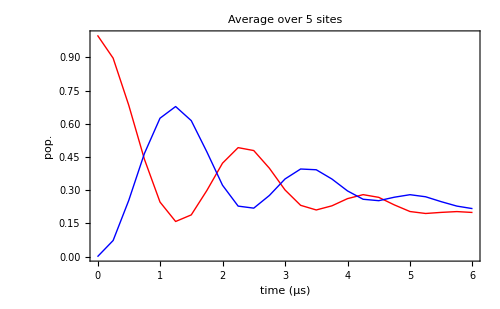

Ωs= 2π 250 MHz;     Ωp=2π 125/6 MHz;     δ_AC=2π 0.864 MHz;     δ_0= -0.6 MHz;     δ_1=1 MHz/μs;     Δ= 2π 7.5 GHz;
 Γ= 2π 100 MHz;    Γ_ground= 2π 0 kHz;    Γ_background= 2π 125/18 kHz;    σ_S=0.02;    σ_P=0.02,    σ_site=0.05

```mathematica
meanTSites=Transpose[Table[meanSites[τ],{τ,0,6,.25}]];
timeList=Table[τ,{τ,0,6,.25}];
ListPlot[{Transpose@{timeList,meanTSites[[1]]},Transpose@{timeList,meanTSites[[2]]}},Joined->True,FrameLabel->{"time (μs)","pop."},PlotLabel->"Average over 5 sites",PlotRange->{0,1}]
StringForm["Ωs= 2π `` MHz;     Ωp=2π `` MHz;     δ_AC=2π `` MHz;     δ_0= `` MHz;     δ_1=`` MHz/μs;     Δ= 2π `` GHz;\n Γ= 2π `` MHz;    Γ_ground= 2π `` kHz;    Γ_background= 2π `` kHz;    σ_S=``;    σ_P=``,    σ_site=``",Ωs/(2π MHz),Ωp/(2π MHz),Round[δac/(2π MHz),.001],start,rate,Δp/(2π GHz), Γ/(2π MHz),Γground/(2π kHz),Γbackground/(2π kHz),ΩsNoise,ΩpNoise,siteNoise]
```

```mathematica
meanT=Transpose[Table[mean[3,τ],{τ,0,8,.5}]];
ListPlot[{Transpose@{timeList,meanT[[1]]},Transpose@{timeList,meanT[[2]]}},Joined->True]
```

## Simulation for optimizing ⟨Ω_Rabi⟩/σ_δ_AC

```mathematica
Length[Range[.1,.15,.01]]
Length[Range[5,20,2]]
```

6

8

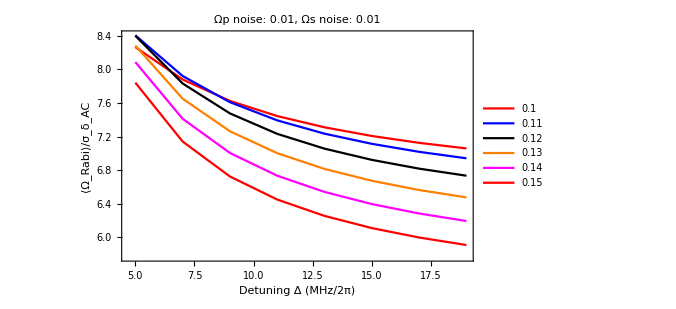

```mathematica
ΩpNoise=0.01;
ΩsNoise=0.01;
randList=Transpose@{Flatten[RandomVariate[NormalDistribution[1,ΩpNoise],{1000,1}]],Flatten[RandomVariate[NormalDistribution[1,ΩsNoise],{1000,1}]]};
Ωs=2π 250 MHz;
ΩrList=Table[Table[1/(2π MHz)Table[(α Ωs^2  j k)/(2 Δ(2π GHz))/.{j-> randList[[i,1]],k-> randList[[i,2]]},{i,1,1000}],{Δ,5,20,2}],{α,.1,.15,.01}];
acList=Table[Table[Table[1/(2π MHz)((j^2 (α Ωs)^2)/(4Δ(2π GHz))+(j^2(11 α Ωs)^2)/(4(Δ(2π GHz)+2π 3.4 GHz))-(k^2 Ωs^2)/(4Δ(2π GHz)))/.{j-> randList[[i,1]],k-> randList[[i,2]]},{i,1,1000}],{Δ,5,20,2}],{α,.1,.15,.01}];
ListPlot[Table[Flatten[Table[Transpose@{acList[[α,i]],ΩrList[[α,i]]},{i,1,8}],1],{α,1,6}],Joined->False,FrameLabel->{"2-photon AC shift (MHz/2π)","Raman Rabi (MHz/2π)"},PlotLegends->{Range[.1,.15,.01]},PlotLabel->"Behavior across α=Ωp/Ωs. Within each color \n the clumps denote different values of Δ"];
ListPlot[Table[Table[{Range[5,20,2][[i]],Mean[ΩrList[[α,i]]]/StandardDeviation[acList[[α,i]]]},{i,1,8}],{α,1,6}],Joined->True,FrameLabel->{"Detuning Δ (MHz/2π)","⟨Ω_Rabi⟩/σ_δ_AC"},PlotLegends->{Range[.1,.15,.01]},PlotLabel->StringForm["Ωp noise: ``, Ωs noise: ``",ΩpNoise,ΩsNoise]]
```